CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\" already exists.

CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\search\\" already exists.

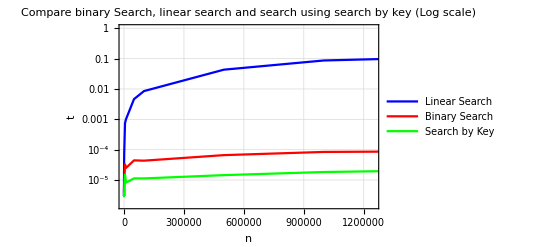

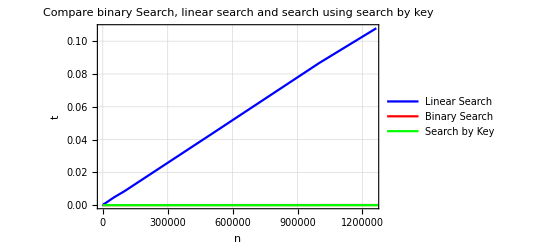

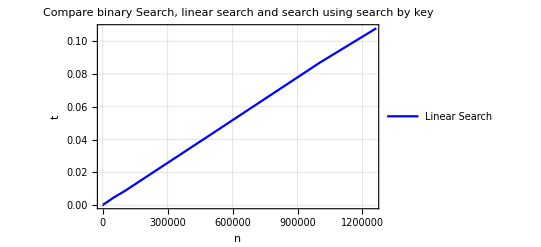

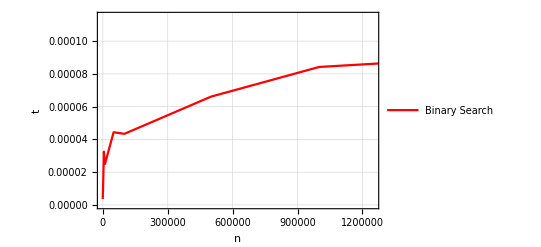

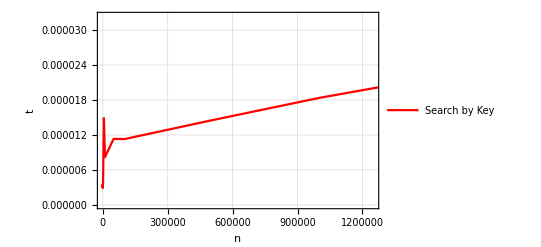

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = CreateDirectory["shown results"];
SetDirectory[workingDirectory];
file= OpenRead["../log_search.txt"];
workingDirectory = CreateDirectory["search"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];

mapSearchResults = filelist[[3;;;;4]];
binarySearchResults = filelist[[2;;;;4]];
linearSearchResults = filelist[[1;;;;4]];
linearSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,linearSearchResults];
binarySearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,binarySearchResults];
mapSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,mapSearchResults];
linearSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,linearSearchResults];
binarySearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,binarySearchResults];
mapSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,mapSearchResults];
Plot1 = Show[ListLogPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"},PlotLabel->"Compare binary Search, linear search and search using search by key (Log scale)", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListLogPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}],
ListLogPlot[mapSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Search by Key"}]]
Plot2 = Show[ListPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"},PlotLabel->"Compare binary Search, linear search and search using search by key", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}],
ListPlot[mapSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Search by Key"}]]
Plot3 = ListPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"},PlotLabel->"Compare binary Search, linear search and search using search by key", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot4 = ListPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}, AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot5 = ListPlot[mapSearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Search by Key"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Linear.gif",Plot3,ImageSize->2048];
Export["Binary.gif",Plot4,ImageSize->2048];
Export["Map.gif",Plot5,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Time"},binarySearchResults[[All,1]]],Join[{"Linear Search"},linearSearchResults[[All,2]]],Join[{"Binary Search"},binarySearchResults[[All,2]]],Join[{"Search by Key"},mapSearchResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Time | Linear Search | Binary Search | Search by Key
5 | 4.97057×10^-6 | 3.61063×10^-6 | 3.24407×10^-6
10 | 3.00947×10^-6 | 3.9332×10^-6 | 2.9105×10^-6
50 | 5.91996×10^-6 | 4.94125×10^-6 | 3.58497×10^-6
100 | 9.64423×10^-6 | 5.41044×10^-6 | 3.04979×10^-6
500 | 0.0000401201 | 7.29823×10^-6 | 3.3467×10^-6
1000 | 0.0000785248 | 8.74615×10^-6 | 3.36503×10^-6
5000 | 0.000750824 | 0.0000324957 | 0.0000149044
10000 | 0.00101266 | 0.0000249958 | 8.19631×10^-6
50000 | 0.00462411 | 0.0000443759 | 0.0000113377
100000 | 0.00851204 | 0.0000434155 | 0.0000112974
500000 | 0.0431631 | 0.000066113 | 0.0000144975
1000000 | 0.0866832 | 0.0000842358 | 0.0000183647
5000000 | 0.408213 | 0.000115276 | 0.0000448451

```mathematica
Export["TableSerch.gif",grid,ImageSize->{2048,720}];
Export["TableSeach.xls",grid,ImageSize->{2048,720}];
```